# Geometry and Other Special Topics

```mathematica
Today
```

Sun 22 Apr 2018

## Geometric regions

Starting from Version 10, Mathematica unifies many aspects of analytical geometry and its mathematical operations under the general notion of a region, a set of points in space that together define a geometric region. These regions can be one-, two- or more-dimensional, and they can be built bottom-up from simpler regions using various transformations and constructive geometry operations.

For defining your bread-and-butter shapes that you would have encountered in high school geometry, several primitives are already available in the language itself. You can look up the parameters required by each shape from the Mathematica documentation, but this is pretty straighforward as they follow mostly common sense. Just like everything else, shapes are expressed and manipulated as symbolic expressions by Mathematica’s knowledge base of rules and patterns. To display these shapes, use the function RegionPlot that can display any individual region or a set of regions. First, some common one-dimensional shapes that ought to be familiar to every schoolchild from eight to eighty.

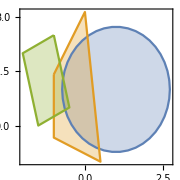

```mathematica
sh1 = Disk[{1, 1}, Sqrt[3]];
sh2 = Polygon[{{-1, -1/3}, {-1, Sqrt[2]}, {0, π}, {1/2, -1}}];
sh3 = Parallelogram[{-2, 2}, {{1, 1/2}, {1/2,-2}}];
RegionPlot[{sh1, sh2, sh3}, ImageSize -> Small]
```

Similarly, there are plenty of built-in primitives for the familiar three-dimensional shapes.

```mathematica
sh4 = Pyramid[{{-1, -1, 0}, {-1, 3/2, 0}, {1, π, 0}, {1, -1/3, 0}, {0,0,1}}];
sh5 = Ellipsoid[{0,2.5,0}, {1/2, 1/3, 1/4}];
sh6 = Cylinder[{{0, -1, -1}, {0, 1, -1}}, 1];
RegionPlot3D[{sh4, sh5, sh6}, ImageSize -> Small]
```

-Graphics3D-

Constructive solid geometry operations union, intersection and difference can be used to combine arbitrary regions in an arbitrary fashion. Lengths, areas and volumes of regions are unified under one function RegionMeasure.

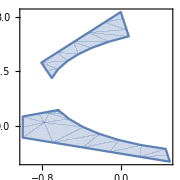

```mathematica
sh7 = RegionDifference[sh2, RegionUnion[sh1, sh3]];
RegionPlot[sh7, ImageSize -> Small]
```

The full symbolic form of that area is pretty complicated, so let’s just look at numerical approximation.

```mathematica
N[RegionMeasure[sh7], 6]
```

1.20859

Let’s do a bit simpler example, this one demonstrating the boundaries of the given region.

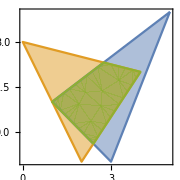

```mathematica
mypol1=Polygon[{{1,1},{5,4},{3,-1}}];
mypol2=Polygon[{{0,3},{4,2},{2,-1}}];
RegionPlot[{mypol1,mypol2,RegionIntersection[mypol1,mypol2]},PlotStyle->Opacity[0.5], ImageSize -> Small]
```

```mathematica
ArcLength[RegionBoundary[RegionIntersection[mypol1,mypol2]]]
```

1/80 (175+112 √2+64 √13+25 √17)

The coolest thing of all this is that our old friends Integrate, NIntegrate, Solve, Minimize and Maximize can be constrained to operate on arbitrary regions. The measure of a region is just special case of integration where you integrate the constant 1 over that region. We can use that to verify that the function ArcLength works correctly.

```mathematica
Integrate[1, {x, y} ∈ RegionBoundary[RegionIntersection[mypol1,mypol2]]]
```

1/80 (175+112 √2+64 √13+25 √17)

```mathematica
Maximize[Sqrt[x] - x y, {x, y} ∈ RegionIntersection[mypol1, mypol2]]
```

{-2/25 (-12-5 √15),{x→12/5,y→-5/12 (-2 √(3/5)-2/25 (-12-5 √15))}}

One more way to do all that stuff would be to use the function Boole to convert a truth value to a number 0 or 1.

```mathematica
Integrate[Boole[{x, y} ∈ RegionBoundary[RegionIntersection[mypol1,mypol2]]], {x, -5, 5}, {y, -5, 5}]
```

0

Whoops: in two-dimensional integration, the integral over a one-dimensional curve will be zero. Let’s try that again, this time over the two-dimensional intersection region.

```mathematica
Integrate[Boole[{x, y} ∈ RegionIntersection[mypol1,mypol2]], {x, -5, 5}, {y, -5, 5}]
```

623/160

The same technique could also be useful in restricting a plot to the given region, although this might be a bit slow and numerically inaccurate.

```mathematica
Plot3D[0.1+(3 + x^2 - y^2) * Boole[{x, y} ∈ mypol1], {x, 0, 5}, {y, 0, 5}, Filling-> Axis, ColorFunction -> "RustTones", ImageSize -> Small]
```

-Graphics3D-

Instead of merely using the predefined geometric primitives, arbitrary regions can be defined as implicit regions, that is, the set of points for which the given condition is true. Here, a variation of a superellipse of order 4.

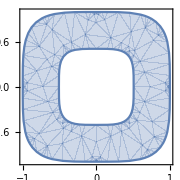

```mathematica
super4 = ImplicitRegion[1/15 ≤ x^4 + y^4 ≤ 1, {x, y}];
RegionPlot[super4, ImageSize -> Small]
```

```mathematica
RegionMeasure[super4]
```

-1/(15 √π)2 (-14^(1/4) √(15 π)+√15 Gamma[1/4] Gamma[5/4]-60 Gamma[5/4]^2+2 15^(3/4) √π Hypergeometric2F1[-1/4,1/4,5/4,1/15]-15^(3/4) √π Hypergeometric2F1[1/4,3/4,5/4,1/15])

```mathematica
N[%]
```

2.75071

Regions can be discretized into a mesh of simpler shapes with the function DiscretizeRegion. As you can see from the numerical approximation of the area, approximating a non-polygonal region with triangles necessarily changes its shape on the edges, as one would need an infinite number of triangles to follow a curved edge.

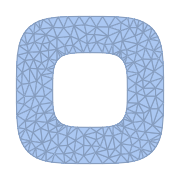

```mathematica
drsuper4 = DiscretizeRegion[super4]
```

```mathematica
RegionMeasure[drsuper4]
```

2.7476

Like all these functions that pack a big punch under the hood, the normally reasonable default behaviour can be modified with a bevy of options. The more points the mesh contains, the more accurately it will approximate the original region.

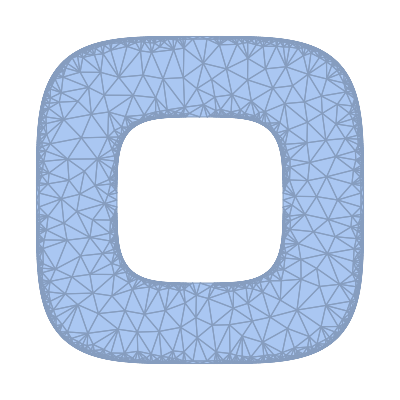

```mathematica
DiscretizeRegion[super4, PrecisionGoal -> 7]
```

What a smart little algorithm, producing more precision in the places of the region where it is needed, and using larger triangles in the internal areas.

```mathematica
RegionMeasure[%]
```

2.75072

As an exercise of recursion, we can program our own quadtree style subdivision algorithm. The rectangle is repeatedly subdivided into four smaller rectangles as long as the rectangle contains points from both outside and inside the arbitrary region passed as second argument. The subdivision is performed recursively up to the third argument, the integer depth. The handy function SignedRegionDistance computes the minimum distance from the boundary of the region to the given point so that if that point is outside the region, the distance is positive, and if the point is inside the region, the distance is negative. The result of quadtree is a list of lines that form the boundary of the rectangles produced by the subdivision. (The smart little function RegionBoundary already knows that the boundary region of any polygon is a list of lines.)

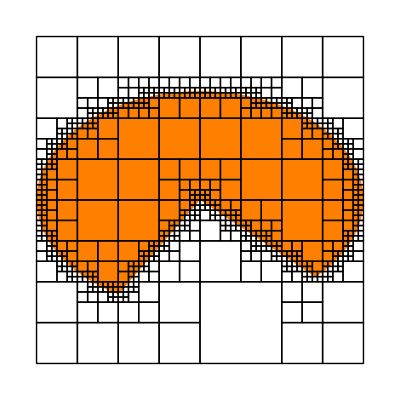

```mathematica
quadtree[rect_, reg_, 0] := RegionBoundary[rect];
quadtree[rect_, reg_, d_] := Module[{rw, rh, center},
rw = (rect[[2]][[1]] - rect[[1]][[1]]) /2;
rh = (rect[[2]][[2]] - rect[[1]][[2]]) / 2;
center = rect[[1]] + {rw, rh};
If[Abs[SignedRegionDistance[reg, center]] > Sqrt[rw^2 + rh^2], 
RegionBoundary[rect],
Flatten[{
quadtree[Rectangle[rect[[1]], center], reg, d-1],
quadtree[Rectangle[rect[[1]] + {rw, 0}, rect[[1]] + {2*rw, rh}], reg, d-1],
quadtree[Rectangle[rect[[1]] + {0, rh}, rect[[1]] + {rw, 2*rh}], reg, d-1],
quadtree[Rectangle[center, rect[[1]] + {2*rw, 2*rh}], reg, d-1]
}]
]
]

sh := Disk[{1/2, 1/2}, {1/2, 1/3}, {-π/4, 4π/3}];
Show[{Graphics[{Orange,sh}],Graphics[{EdgeForm[Dashed],quadtree[Rectangle[{0,0},{1,1}], sh, 6]}]}]
```

Another way to define arbitrary regions is to use a parametric representation so that the region contains the points produced by the given functions from the parameters that go through a range of values. In the plot of the Lissajous curve, you can try changing the coefficients in the sine and cosine functions to see their effect on the shape of the curve.

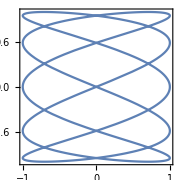

```mathematica
RegionPlot[ParametricRegion[{Cos[5θ],Sin[2θ]},{{θ,0,2 π}}], ImageSize -> Small]
```

Computational geometry poses questions and answers for sets of points in spaces of various dimensions. One of the most important question is finding the convex hull of the given set of points, that is, the minimal convex polygon that contains all of the points.

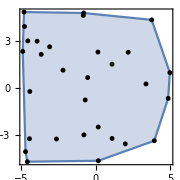

```mathematica
points = RandomReal[{-5, 5}, {30, 2}];
Show[RegionPlot[ConvexHullMesh[points]], ListPlot[points, PlotStyle -> Black], ImageSize -> Small]
```

For a set of points in space, the functions VoronoiMesh and DelaunayMesh produce its Voronoi mesh and Delaunay triangulation. The Voronoi mesh of a set of points partitions the space into regions whose points are closer to that point than to any other point in that set. For the points on the convex hull of the set, the resulting region is infinite. Connecting the points that share an edge in the Voronoi mesh produces the Delaunay triangulation, the best way to triangulate the points so to avoid thin “sliver” triangles that are computationally problematic and difficult to render. The Delaunay triangulation has the curious property that if you draw the unique circle through the three points of each triangle, no other point in the original set falls inside this circle.

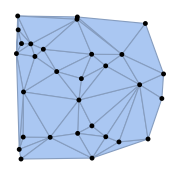

```mathematica
Show[DelaunayMesh[points], ListPlot[points, PlotStyle -> Black], ImageSize -> Small]
```

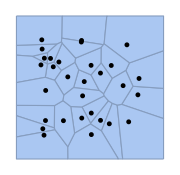

```mathematica
Show[VoronoiMesh[points], ListPlot[points, PlotStyle -> Black], ImageSize -> Small]
```

The functions VoronoiMesh and DelaunayMesh produce MeshRegion expressions as results, but you could just as well define your own MeshRegion with of a set of points that are shared by the polygons and other regions that will then constitute the mesh. (A mesh can even be three-dimensional and consist of three-dimensional regions, or even mix regions of different dimensionalities together!) The functions MeshCells, MeshCoordinates and MeshPrimitives can then be used to extract that information from a mesh. Simple substitutions will then allow us to render the mesh region primitives as something else, such as filled and closed B-splines. (The idea for this example was shamelessly borrowed from one of the thousands of demonstrations in Wolfram Demonstrations Project.) The function FilledCurve converts any closed curve into a two-dimensional region.

```mathematica
Show[{Graphics[
MeshPrimitives[VoronoiMesh[points],2] /. Polygon[pts__] :> {RGBColor[RandomReal[{1/4,3/4}, 3]], FilledCurve[BSplineCurve[pts, SplineClosed -> True]]}], Graphics[{Black, PointSize[.02], Point[points]}]}, ImageSize -> Medium]
```

-Graphics-

```mathematica
% /. BSplineCurve -> BezierCurve
```

-Graphics-

Intervals are an important special case of regions on the one-dimensional real number axis. Mathematica can express intervals symbolically with the function Interval. The intervals defined with this function play along nicely with the other functions in Mathematica, and can therefore be used to investigate the ranges or the limit behaviour of various functions.

```mathematica
Interval[{1, 2}] + Interval[{3, 4}]
```

Interval[{4,6}]

```mathematica
Sin[%]
```

Interval[{-1,Sin[6]}]

```mathematica
(x^3 - 2x + 1) /. x-> Interval[{1, 10}]
```

Interval[{-18,999}]

```mathematica
Limit[Sin[x^2] / 2, x-> Infinity]
```

Interval[{-1/2,1/2}]

```mathematica
Limit[Sin[1/x], x -> 0]
```

Interval[{-1,1}]

## Geodesy and other forms of here-sy

The real-world knowledge base of Mathematica comes with functions to do all kinds of geodesic computations, in the original sense of the word “geometry” referring to measuring the Earth and its parts, packed into a couple of powerful functions that do essentially all of the work. Expressions of the type GeoPosition represent particular geographic positions as tuples of latitude and longitude, with an optional altitude and time arguments thrown in for a good measure. Entities that reside in the physical Earth know their geographical positions and can be given as arguments directly to GeoPosition, or we can use the function EntityValue to extract the position properties just like with any other properties.

```mathematica
cntower = Entity["Building", "CNTower"];
cnpos = GeoPosition[EntityValue[cntower, "Position"]];
```

The general-purpose map rendering function GeoGraphics can be used to create a map around some particular GeoPosition or a list of geographical entities and primitives, with a multitude of cool options to control the style of the result. The geographical primitive GeoMarker is rendered as a pin that displays its exact position. The option GeoRange can be used to control the scale of the map that GeoGraphics renders around that position. This option can be given as a distance of some suitable Quantity, or a context-dependent argument such as “Country” or “World” and let Mathematica take it from there.

```mathematica
GeoGraphics[{cnpos, GeoMarker[cnpos]}, GeoRange -> Quantity[1, "Kilometers"]]
```

-Graphics-

If you were one of those crazy Russian climbers we can see on YouTube, coolly standing on the very top of the CN Tower needle, how far could you see? The function GeoVisibleRegion tells us the answer once we modify the GeoPosition to include the altitude component.

```mathematica
GeoGraphics[GeoVisibleRegion[cnpos /. {lat_, lon_} -> {lat, lon, EntityValue[cntower, "Height"]}]]
```

-Graphics-

Suppose the CN Tower stretched to be 10 miles high? You could see all the way to Ottawa, then, and almost to New York City.

```mathematica
GeoGraphics[GeoVisibleRegion[cnpos /. {lat_, lon_} -> {lat, lon, Quantity[10, "Miles"]}]]
```

-Graphics-

The GeoElevationData knowledge base can be used to acquire the elevation of the given position, as measured from the sea level. Now the altitude isn’t quite as frightful.

```mathematica
GeoElevationData[cnpos]
```

83.

The functions GeoIdentify and GeoNearest can be used to extract information from Mathematica’s geodesic knowledge base. GeoIdentify will find the entities of given type that the geometric position belongs to, whereas GeoNearest finds the given number of entities of certain type that are nearest to that position.

```mathematica
GeoIdentify[All, cnpos]
```

{America/Toronto,world,Canada,Ontario, Canada,CN Tower,GMT-5,Toronto, Ontario, Canada,North America}

```mathematica
GeoNearest["City", cnpos, 10]
```

{Toronto,Mississauga,Vaughan,Richmond Hill,Markham,Brampton,Oakville,Pickering,Nobleton,Ajax}

For discovery and enumeration, the function GeoEntities produces the list of all geometric entities of certain type that are partially (or fully, if using the option “FullyContained” -> True) contained inside some larger geometric entity. As an example, let us discover and map all the mountains in Alaska. The function GeoGraphics is usually smart enough to automatically choose a scale that best fits the geographical positions or entities that it renders.

WolframAlphaQueryParseResults

Entity[AdministrativeDivision,{Alaska,UnitedStates}]

```mathematica
GeoEntities[%, "Mountain"]
```

{Mount Mather,Mount Alice,Flattop Mountain,Mount Chamberlin,Camp 4 Peak,Mount Troy,Bold Peak,Mount Orville,Lewis Peak,Aniakchak,Mount Michelson,Dinglishna Hill,Denali,Mount Dall,Wedge Peak,Brooks Mountain,Devils Thumb,Mount Neacola,Mount Ripinski,Aello Peak,Mount Hesperus,Tolch Rock,Mount Foraker,Flat Top Mountain,Mount Capps,Moose's Tooth,Mount Valhalla,Mount Moffit,Mount Bendeleben,Mount Bona,Mount Katmai,Mount Igikpak,Middle Triple Peak,Peters Dome,Mount Brooks,Mount Blachnitzky,Mount POW/MIA,Deer Mountain,Mount Marcus Baker,Auke Mountain,Truuli Peak,Mount Pendleton,Devils Desk,Mount Crosson,Rosebud Summit,Mount Torbert,Mount Crillon,Paradise Peak,Gastineau Peak,Byron Peak,Mount Huntington,Mount Bassie,Mount Wilbur,Mount Eldridge,Mount Deception,Mount Sanford,Mount Silvertip,Limestack Mountain,Mount Deborah,Ptarmigan Peak,Mount Dickey,Bashful Peak,Mount Tripyramid,Camp 15 Peak,Mount Billy Mitchell,Mount Root,Mount Carpe,Gurney Peak,Mount Drum,Lituya Mountain,Mount Furuhelm,Mount Saint Elias,Mount Wrangell,Peak 7510,Silverthrone,Table Top Mountain,Montana Peak,Cape Mountain,Mount Tatum,Mount Salisbury,Mount Michelson,Mount Russell,Manzanita Peak,Mount Osborn,Mount Quincy Adams,Mount Bear,Mount Eddy McKenney,Cockedhat Mountain,Mount Palmer,Mount Verstovia,Mount Mend Carp,Kichatna Spire,White Princess,Army Peak,Thibedeau Mountain,Mount Gallatin,Kahiltna Peaks,Mount Arrowhead,Mount Roberts,Mount Hayes,Mount Susitna,Mount Kimball,Mount Prindle,Wiki Peak,Bird Peak,Mount Hunter,Pioneer Peak,Mount Steller,Mount Stevens,Kahiltna Dome,Mount Cook (Boundary Peak 182),Moose Mountain in Alaska,Mount Fairweather,Amherst Peak,Mount Blackburn,Peak 8620,Eagle Peak,Mount Isto,Mount Marathon,Mount Natazhat,Mount McGinnis,Phoenix Peak,Mount Gannett,Mount Thor,Mount Schou,Augustin Peak,Mount Miller,Peak 5390,Fake Peak,Avalanche Spire,Scott Peak,Dipyramid,Mount Koven,Thetis Mound,Annex Peak,University Peak,Mount Juneau,Tukgahgo Mountain,Boundary Peak 96,Mount Dan Beard,Polar Bear Peak,Ear Mountain,Matanuska Peak,Nasak,Twin Peaks}

```mathematica
GeoGraphics[GeoMarker[%]]
```

-Graphics-

Mathematica’s built-in geometric primitives such as Polygon are able to directly handle and represent geometric coordinates. When rendering large areas with GeoGraphics, different styles of maps such as street maps or relief maps can be used. A relief map uses the elevation data to generate the colour for each pixel.

WolframAlphaQueryParseResults

France

```mathematica
francegon  = Polygon[%];
GeoGraphics[{GeoStyling["ReliefMap"],francegon}, GeoBackground-> None]
```

-Graphics-

For sufficiently large geographical entities, using a different type of GeoProjection can potentially make a huge difference. There are quite a few of these, all stored in the GeoProjectionData knowledge base. Your choice of projection determines which properties of the original sphere are maintained in the projection. No projection can possibly maintain all possible properties for the simple reason that the surface of the sphere simply is not a two-dimensional rectangle, but a completely different thing geometrically. The following table gives a small taste of all the projections available, showing nine randomly chosen projections of the spherical projections family.

```mathematica
Grid[Partition[Table[Column[{GeoGraphics[{}, GeoRange -> "World", GeoProjection -> p, GeoGridLines -> Automatic], Text[p]}, Center], {p, RandomSample[GeoProjectionData["Spherical"], 9]}], 3]]
```

-Graphics-
EckertIII | -Graphics-
Stereographic | -Graphics-
LambertConformalConic
-Graphics-
Polyconic | -Graphics-
Albers | -Graphics-
WinkelTripel
-Graphics-
Sinusoidal | -Graphics-
LambertAzimuthal | -Graphics-
MillerCylindrical

As an alternative to GeoGraphics, the function GeoListPlot can also be used to generate a map that contains all of the geographic entities of its argument list. The entities don’t need all be the same type, but you can freely mix all sorts of entities in the same map. Just like GeoGraphics, this function is also smart enough to choose a suitable scale automatically. To show it in action, let us draw a map of all the countries of OPEC and their capital cities, labelled with their names.

WolframAlphaQueryParseResults

Organization of Petroleum Exporting Countries

```mathematica
opeccountries = EntityList[%]
```

{Algeria,Angola,Ecuador,Iran,Iraq,Kuwait,Libya,Nigeria,Qatar,Saudi Arabia,United Arab Emirates,Venezuela}

```mathematica
opeccapitals = EntityValue[ opeccountries, "CapitalCity"]
```

{Algiers,Luanda,Quito,Tehran,Baghdad,al-Kuwayt,Tripoli,Abuja,Doha,Riyadh,Abu Dhabi,Caracas}

```mathematica
GeoListPlot[{opeccountries, opeccapitals}, GeoLabels -> True, ImageSize -> Large, LabelStyle->Directive[8,Italic]]
```

-Graphics-

Each country is a geographical entity, but it does also have a single geographical position, defined as the position of its center of mass.

```mathematica
opecpos = GeoPosition[opeccountries]
```

GeoPosition[{{28.,3.},{-12.5,18.5},{-2.,-77.5},{32.,53.},{33.,44.},{29.514,48.025},{25.,17.},{10.,8.},{25.5,51.25},{25.,45.},{24.,54.},{8.,-66.}}]

Just out of curiosity, what is on the opposite side of the Earth for those positions? Equador and Venezuela end up somewhere in Indonesia, but the Middle East coordinates all mirror into the vast and empty Pacific Ocean that, if you look at Earth at an actual globe instead of the typical two-dimensional map, fills about half of the Earth. Notice the asymmetry in the formula that computes the antipodal coordinates for the given latitude and longitude. The former can simply be negated, but the latter has to be offset by 180.

```mathematica
GeoGraphics[Apply[GeoMarker,opecpos /. {lat_, lon_} -> {-lat, 180+lon}], ImageSize -> Large]
```

-Graphics-

The function GeoPath can be used to generate a geometric path that traverses a sequence of geometric positions. It wouldn’t really make any difference on the street view scale inside one city, but on the global scale, the geodesic, rhumb and great circle paths will be quite different.

```mathematica
GeoGraphics[{GeoPath[opecpos, "Geodesic"]}]
```

-Graphics-

```mathematica
GeoGraphics[{GeoPath[opecpos, "RhumbLine"]}]
```

-Graphics-

The function GeoDistance calculates the distance between two geographic positions or entities, as measured along the great circle. In the latter case, you can additionally specify whether you are looking for the distance between the closest pairs of points of their borders, or the distance of their centers.

```mathematica
opec5 = Take[opeccountries, 5];
opec5names = EntityValue[ opec5, "Name"]
```

{Algeria,Angola,Ecuador,Iran,Iraq}

```mathematica
TableForm[Table[GeoDistance[c1, c2, DistanceFunction -> "Center"], {c1, opec5}, {c2, opec5} ], TableHeadings->{opec5names, opec5names}]
```

| Algeria | Angola | Ecuador | Iran | Iraq
Algeria | 0. | 4782.44 | 9186.53 | 4802.35 | 3950.01
Angola | 4782.44 | 0. | 10621.7 | 6145.59 | 5718.07
Ecuador | 9186.53 | 10621.7 | 0. | 13874.6 | 13041.3
Iran | 4802.35 | 6145.59 | 13874.6 | 0. | 852.757
Iraq | 3950.01 | 5718.07 | 13041.3 | 852.757 | 0.

## Propositional logic

From the geometry of spaces of arbitrary number of dimensions, we move on to propositional logic and Boolean variables. Propositional logic consists of variables and expressions whose possible values are True and False, easily converted to numbers with the function Boole when needed.

A more than sufficient set of boolean functions would be the classic quintet And, Or, Not, Implies, and Equivalent so that all Boolean functions can be expressed by composition of these functions. In formulas, Mathematica recognizes the shorthand forms ∧, ∨, ¬, ⇒ and ⧦ of mathematical logic for these operators. When producing logical expressions as results, Mathematica for some reason uses the cryptic shorthands &&, || and ! that are used in most programming languages derived from C. (Those languages and these symbols are relics from the era when only the ASCII character set existed, if even that.)

When the result of the entire expression is certain from the first argument, the operators And and Or are guaranteed to short circuit the evaluation so that the second argument will not get evaluated at all. For example, since Or requires at least one of the arguments to be true, if the first argument turns out to be true, the entire expression is certainly true regardless of the value of the second argument. This can make a difference if the second argument has side effects such as output. Every programming language ever created guarantees short circuit evaluation, since that is the only reasonable way things can be.

```mathematica
msg := Module[{},Print["Evaluated!"]; True];
(0 < 1) || msg
```

True

```mathematica
(0 < 1) && msg
```

Evaluated!

True

In addition to this basic set of logical operators, Mathematica naturally has Xor, Xnor, Nand and Nor already defined. It also has a set of useful functions that can create many important Boolean functions on the fly. For example, BooleanCountingFunction creates an expression that evaluates to True if and only if the given number of its arguments are True.

```mathematica
f= BooleanCountingFunction[{2}, {x, y, z}]
```

(x&&y&&!z)||(x&&!y&&z)||(!x&&y&&z)

```mathematica
f /. {x -> True, y-> True, z -> False}
```

True

Every boolean function is fully defined by its truth table. It has 2^kelements for k variables. The following truth table is generated in the evaluation order {True, False} of the possible truth values.

```mathematica
BooleanTable[f, {x, y,z}]
```

{False,True,True,False,True,False,False,False}

That might actually be clearer when shown in proper truth table form. To properly construct this table, we get to combine various operations one- and two-dimensional lists, so it’s a double gain for the educational purposes.

```mathematica
Grid[Join[{Map[Style[#, Bold]&,{"x", "y", "z", "f"}]}, Partition[Flatten[Riffle[Tuples[{True, False}, 3],BooleanTable[f, {x, y, z}]]],4]], Frame->{All, False}]
```

x | y | z | f
True | True | True | False
True | True | False | True
True | False | True | True
True | False | False | False
False | True | True | True
False | True | False | False
False | False | True | False
False | False | False | False

Since propositional logic is exactly equal to all possible polynomial-time computation in power, and the problem of deciding whether the given Boolean formula is satisfiable (that is, at least one assignment of truth values for its propositions makes the entire formula to be True) is famously NP-complete so that no polynomial-time algorithms are known to solve this problem, it is no surprise that the same formulas can be expressed in a multitude of equivalent ways. The function BooleanConvert can transform any expression to and from different classic forms. Different ways to define the same formula can shed additional light to how that formula works.

```mathematica
BooleanConvert[f, "CNF"]
```

(!x||!y||!z)&&(x||y)&&(x||z)&&(y||z)

```mathematica
BooleanConvert[f, "IMPLIES"]
```

(x⇒!((y⇒z)⇒!(!y⇒!z)))⇒!(!x⇒(y⇒!z))

The function BooleanMinimize finds the equivalent expression of minimum length. Because of NP-completeness of this problem, this can take an exponential time. (Otherwise, we could easily check if a formula is satisfiable by checking whether its minimum length form is something else than False, earning ourself a million dollars and worldwide fame for solving the second one of the five Millenium Problems.) But for short formulas, this will be done in a jiffy.

```mathematica
BooleanMinimize[f]
```

(x&&y&&!z)||(x&&!y&&z)||(!x&&y&&z)

Satisfiability checking and generating the given number of satisfying truth value assignments are available as functions.

```mathematica
SatisfiableQ[f]
```

True

```mathematica
SatisfiabilityCount[f]
```

3

```mathematica
SatisfiabilityInstances[f, {x, y, z}, 8]
```

{{True,True,False},{True,False,True},{False,True,True}}

Let’s see if we can solve “One True Sentence” by the anti-art activist Henry Flynt. Using the symbol s_i to denote the proposition “The sentence number i is true”, we construct the formula piecemeal and see how many satisfiable solutions exist for it. There should exist precisely as many solutions as there are sentences on the wall, since even though all those sentences are identical, exactly one of them is true! Of course, the purpose of this anti-artwork is to demonstrate what happens when logical sentences are twisted to confront the semantic difference between “X” and “X is true” and “It is true that X is true”, all expressed on different levels of logic and metalogic. (The paradox can be resolved here by noticing that despite the appearances, these sentences are not identical, since their position on the wall is a hidden parameter that distinguishes between them.)

```mathematica
Import["http://www.henryflynt.org/photos/artworks/onetruesentence.jpg"]
```

-Graphics-

```mathematica
henry[n_] := Module[{sentences, f, g},
sentences = Table[Subscript[s, i], {i, 1, n}];
f = True;
Do[
g = BooleanCountingFunction[{0}, Delete[Table[sentences[[j]], {j, 1, n}], i]];
f = f ∧ (sentences[[i]] ⇒ g) ∧ (g ⇒ sentences[[i]])
,{i, 1, n}
];
SatisfiabilityCount[f, sentences]
];

henry[56]
```

56

Coming back to computational geometry for a moment, BooleanRegion generalizes the computational geometry operations union, intersection and difference for arbitrary propositional logic formulas. To illustrate, let us plot the region of the plane whose points belong to exactly one of the three regions given as a list as the second argument to BooleanRegion.

```mathematica
ℜ = BooleanRegion[BooleanCountingFunction[{1}, 3], {Triangle[{{1, 1}, {3, 2}, {2, 4}}], Disk[{3/2, 3/2}, 1], Disk[{3, 2}, Sqrt[2]]}]
```

BooleanRegion[BooleanCountingFunction[{1},3][#1,#2,#3]&,{Triangle[{{1,1},{3,2},{2,4}}],Disk[{3/2,3/2},1],Disk[{3,2},√2]}]

Note the use of {1} instead of 1 as the first parameter, to require the point to belong to exactly one of the following regions, no more and no less. Without the curly braces the resulting region would be infinite, since it would also contain all the points that belong to zero of the three given shape regions. But now the resulting region is nice and small:

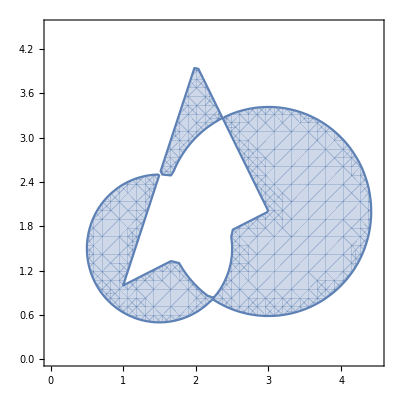

```mathematica
RegionPlot[{x,y} ∈ℜ, {x, 0, 4.5}, {y, 0, 4.5}]
```

Computational geometry functions can analyze Boolean regions like any other regions. The analytical solution is quite hairy, so for now we shall again satisfy ourselves with the numerical solution.

```mathematica
N[RegionMeasure[ℜ], 6]
```

6.42137

## Solving problems with logic

In principle, propositional logic can be used to express any computation, as can be seen from the fact that the physical computer processor, below the level of machine code instructions, does everything with logic gates. In the theory of computability, a given instance of any decision problem that allows a polynomial-time algorithm expressed in Mathematica, C, Java or any programming language whatsoever, can always be converted in polynomial time into a propositional logic formula whose evaluation produces the same answer as the original decision algorithm. Similarly, a given instance of any search problem that allows the offered solution to be verified by a polynomial-time algorithm can be converted to an equivalent instance of satisfiability of propositional logic.

Consider the problem of graph 3-colouring, a famous NP-complete combinatorial problem on undirected graphs. Your task is to colour the vertices of the given graph using three colours numbered { 1, 2, 3 } so that no two neighbouring vertices, that is, connected by an edge, are given the same colour. This may or may not be possible for the given graph. To convert this problem into a propositional logic formula for the given graph of v vertices, we generate a total of 3v separate propositions x_vc (the auxiliary function gp[v_, c_] given below does this for the given v and c) that each represent the proposition “Vertex v is coloured with the colour c”. We then create a conjunction of formulas that effectively say “This vertex has exactly one colour” and “The vertices connected by this edge have a different colour”, and combine these formulas into one giant formula that Mathematica will then simplify. Since the graph 3-colouring problem is NP-complete, this algorithm is inherently exponential in the worst case, no matter which way we attempt to tackle it.

```mathematica
gp[v_, c_] = Subscript[x, 3*(v-1) + c];
threecolouring[g_] := Module[{v, f, props},
v = VertexCount[g];
f = True; 
Scan[(f = f ∧ BooleanCountingFunction[{1}, {gp[#, 1], gp[#,2], gp[#,3]}])&, VertexList[g]];
Scan[
(f = f ∧ ¬(gp[#[[1]], 1] ∧ gp[#[[2]],1]) ∧ ¬(gp[#[[1]], 2] ∧ gp[#[[2]],2]) ∧ ¬(gp[#[[1]], 3] ∧ gp[#[[2]],3]))&, EdgeList[g]];
f
];
```

The function Scan is a handy variation of Do that loops through the elements of the given list, and executes its first argument function for each element. Having defined the function threecolouring, we can try it for a randomly constructed graph, using a suitable random distribution of edges to make a solution exist. (If a graph has any subgraph of k vertices that are all connected to each other, then obviously it cannot have a colouring for k - 1 colours.) To strengthen the faith on the fact that our construction of propositional logic formulas to encode the graph colouring problem was correct, we also use the built-in graph analysis function ChromaticPolynomial to verify the number of 3-colourings.

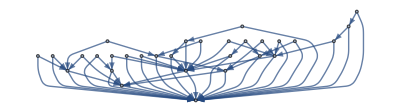

48

48

```mathematica
g = RandomGraph[PriceGraphDistribution[30,2,1]]
SatisfiabilityCount[threecolouring[g]]
ChromaticPolynomial[g, k] /. k-> 3
```

Project Euler, the famous programming exercise website, offers a similar combinatorial problem that we can solve with propositional logic. The puzzle number 161 asks you to count the number of ways that some integer rectangle (whose area must be divisible by 3) can be completely filled with triominoes, that is, the six possible polyominoes of size three. You are allowed to reuse each possible triomino shape as many times as you please.

We can convert this problem to an equivalent problem in propositional logic by again defining a set of propositions p_xyt of the form “Cell (x, y) is the starting point of a triomino t”. In the list trionos, each element contains the cells that are covered by that triomino, in addition to the origin cell that is the starting point of that triomino.

```mathematica
trionos = { 
{ {+1, 0}, {0, +1} },
{ {0, +1}, {+1, +1} }, 
{ {+1, 0}, {+2, 0} },
{ {0, +1}, {0, +2} },
{ {+1, 0}, {+1, +1} },
{ {+1, -1}, {+1, 0} }
};
inside[{x_, y_}, w_, h_] := x > 0 && y > 0 && x ≤ w && y ≤ h;
gp[x_, y_, type_, w_] = Subscript[p, 7 * (((y-1)* w + x)-1) + type];
```

The propositional logic formula that represents this mess is created in three stages. First, the conjunction of all formulas that say “The cell (x, y) must be either empty or the starting point of exactly one triomino shape”, easily produced by the BooleanCountingFunction utility. Second, all the formulas that say “If there is a triomino t starting at cell (x, y), no part of this triomino may not extend outside the rectangle, and the cells that this triomino covers may not have another triomino starting there.” Third, all the formulas that say “If the cell (x, y) is empty, there must exist exacly one other cell that is the starting point of some triomino that covers this cell”, again constructed easily with BooleanCountingFunction.

```mathematica
trionofill[w_, h_] := Module[{f, g, nx, ny, props},
f = True;
Do [
f = f ∧ BooleanCountingFunction[{1}, Table[gp[x, y, type, w], {type, 0, 6}]],
{x, 1, w}, {y, 1, h}
];
Do [
Do[
nx = x + np[[1]];
ny = y + np[[2]];
If[inside[{nx, ny}, w, h],
f = f ∧ (gp[x, y, t, w] ⇒ gp[nx, ny, 0, w]),
f = f ∧ ¬gp[x, y, t, w];
] 
, {t, 1, Length[trionos]}, {np, trionos[[t]]}
],
{x, 1, w}, {y, 1, h}
];
Do [
g = {};
Do[
nx = x - np[[1]];
ny = y - np[[2]];
If[inside[{nx, ny}, w, h],
g = Append[g, gp[nx, ny, t, w]],
Null
]
, {t, 1, Length[trionos]}, {np, trionos[[t]]}
];
f = f ∧ (gp[x, y, 0, w]⇒ BooleanCountingFunction[{1}, g]);
,{x, 1, w}, {y, 1, h}
];
f
];

SatisfiabilityCount[trionofill[9, 2]]
```

41

The triomino filling example illustrates the difficulties inherent in trying to even talk about complex problems with propositional logic. Propositional logic has no mechanism to express concepts such as “Every cell must be covered by exactly one triomino” in a single sentence like we do in English, but forces us to build this formula piecemeal from simples propositional sentences “Cell (1, 1) is covered by exactly one triomino”, “Cell (1, 2) is covered by exactly one triomino”, and so on, where each part “... is covered by exactly one triomino” further expands into a flock of propositional formulas, each one necessarily constructed separately and cannot be shared by the other parts of the formula since they all use different proposition names. The language of the propositional logic, as powerful as it is, simply lacks the ability to identify some set of things and make universal and existential claims about the members of those sets. Every proposition is an island.

To rectify this situation, propositional logic generalizes to far more powerful and expressive first order predicate logic with the quantifier functions ForAll and Exists, possibly entered with the logical shorthand symbols ∀ and ∃. The function Resolve can be used to perform logical resolution on such formulas. The first order predicate logic resolution process is complete so that if a formula is true by definition in all possible worlds where the assumed axioms are known to be true, the resolution algorithm can always determine this to be so, although there really can be no limit even in theory how long this resolution process might take. The formula given as argument to Resolve will either then be identified as True or False, or the resolution mechanism simplifies it to a logical condition for the formula to be True.

```mathematica
Resolve[ForAll[x, Exists[y, y > x]], Integers]
```

True

```mathematica
Resolve[Exists[y, ForAll[x, y > x]], Integers]
```

False

When does a quadratic equation have a real solution?

```mathematica
Resolve[Exists[x, a x^2 + b x + c == 0], Reals]
```

(a==0&&b≠0)||(a==0&&c==0)||(a≠0&&-b^2+4 a c≤0)

In the analysis of efficiency of algorithms, we want algorithms to be linear time rather than quadratic time, since regardless of the hidden constant factors, there necessarily exists a problem size n so that for problems of that size or larger, the linear time algorithm is faster measured in terms of absolute time (also called “the wall clock time”).

```mathematica
Resolve[ForAll[c1, ForAll[c2, c1 > 0 && c2 > 0 ⇒Exists[n, n > 0 && ForAll[n2, n2 > n ⇒ c1 * n < c2 * n^2]]]], Reals]
```

True

In the popular newspaper puzzle of sudoku, which cells are connected in the sense that they are not allowed to contain the same digit?

```mathematica
id[x_] := x ∈ Integers ∧ 0 < x ∧ x < 10;
samerow[x1_, y1_, x2_, y2_] := x1 == x2;
samecol[x1_, y1_, x2_, y2_] := y1 == y2;
samesquare[x1_, y1_, x2_, y2_] :=
Floor[(x1-1) / 3]== Floor[(x2-1) / 3] && Floor[(y1-1) / 3]== Floor[(y2-1) / 3];
connected[x1_, y1_, x2_, y2_] := id[x1] ∧ id[y1] ∧ id[x2] ∧ id[y2] ∧ (x1 ≠ x2 ∨ y1 ≠ y2) ∧ (samerow[x1, y1, x2, y2] ∨ samecol[x1, y1, x2, y2] ∨ samesquare[x1, y1, x2, y2])
```

Reduce and Resolve can now be used to produce formulas to check, for example, whether the cell (x, y) is logically connected to the cell (4, 4).

```mathematica
Reduce[connected[4,4,x, y]]
```

(x==1&&y==4)||(x==2&&y==4)||(x==3&&y==4)||(x==4&&y==1)||(x==4&&y==2)||(x==4&&y==3)||(x==4&&y==5)||(x==4&&y==6)||(x==4&&y==7)||(x==4&&y==8)||(x==4&&y==9)||(x==5&&y==4)||(x==5&&y==5)||(x==5&&y==6)||(x==6&&y==4)||(x==6&&y==5)||(x==6&&y==6)||(x==7&&y==4)||(x==8&&y==4)||(x==9&&y==4)

```mathematica
Resolve[connected[4,4,x,y], Integers]
```

x∈Integers&&0<x&&x<10&&y∈Integers&&0<y&&y<10&&(4≠x||4≠y)&&(4==x||4==y||(1==Floor[1/3 (-1+x)]&&1==Floor[1/3 (-1+y)]))

However, even predicate logic is powerless to capture the distinction between the two claims “X” and “X is true”, even for something as seemingly simple as integer arithmetic with addition and multiplication. However, predicate logic is powerful enough to capture all of algorithmic computability and can therefore express the claim “X can be proven to be true”. This leads to Gödel’s Incompleteness Theorems about how for any algorithm whatsoever that generates sentences of predicate logic that are true in the standard model of natural numbers, there exists (and can even be effectively constructed) the Gödel sentence of that system. This Gödel sentence is a sentence with a curious property that it is undeniably true for natural numbers, and yet can never be generated by that algorithm.

In other words, for any attempt to capture all mathematical truths soundly into some formal system S that is both strong enough to model integer arithmetic and weak enough so that its operations can be expressed algorithmically, there exists a Gödel sentence that effectively says “This sentence is unprovable in the system S”, making that sentence true (if it were false, that would mean that the sentence is provable in system S, which would make S unsound since false claims can be proven in it) but unprovable in the system S, which makes system S incomplete. (Read that paragraph a couple of times and think about it.)

Speaking of things unsolvable and unknown, let’s find out if Mathematica has heard that Fermat’s Last Theorem was proven true by Andrew Wiles back in 1995, so that there do not exist positive integers x, y and z and an integer exponent n > 2 so that x^n+y^n = z^n. (For n = 2, of course  an infinite number of solutions exist as the three sides of Pythagoran triangles.)

```mathematica
Resolve[Exists[{n, x, y, z}, n > 2 ∧ x>0 ∧ y>0 ∧ z > 0 ∧ x^n + y^n == z^n], Integers]
```

False

Goldbach conjecture (every even integer greater than 2 can always be somehow expressed as a sum of two prime numbers) and Twin prime conjecture (there exist infinitely many prime numbers p so that p + 2 is also a prime number) still remain unsolved. It is still educational to see how the concept of primality these conjectures are expressed using first-order predicate logic. Even though we cannot talk about sets of integers directly, we can express the notion “There exist infinitely many positive integers n so that ϕ(n)” by rewriting it as “For any integer m, there exists an integer n > m so that ϕ(n)”.

```mathematica
prime[n_] := Module[{p,q},
n ∈ Integers ∧ n > 1 ∧ ForAll[{p, q}, (p > 0 ∧ q > 0 ∧ p∈ Integers ∧ q ∈ Integers ∧ p * q == n) ⇒ (p == 1 ∨ q == 1)]
]

Grid[Partition[Table[If[Resolve[{prime[i]}, Integers], Framed[i], i], {i, 1, 100}], 10]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

Even Mathematica can do no better with the next two formulas than throw its cybernetic hands in the air. Since the function prime was defined to be a Module, its local symbols p and q are automatically renamed by tacking a dollar sign and a context identifier after the name, to make sure the name doesn’t conflict the previous definitions of these symbols.

```mathematica
Resolve[ForAll[n, n > 1 ⇒Exists[p, prime[p] ∧ prime[2 n - p]]], Integers]
```

∀_{n}(n>1⇒∃_{p}(p∈Integers&&p>1&&∀_{p$132013,q$132013}(p$132013>0&&q$132013>0&&p$132013∈Integers&&q$132013∈Integers&&q$132013 p$132013==p⇒p$132013==1||q$132013==1)&&2 n-p∈Integers&&2 n-p>1&&∀_{p$132014,q$132014}(p$132014>0&&q$132014>0&&p$132014∈Integers&&q$132014∈Integers&&q$132014 p$132014==2 n-p⇒p$132014==1||q$132014==1)))

```mathematica
Resolve[ForAll[m, Exists[p, p > m ∧ prime[p] ∧ prime[p+2]]]]
```

∀_{m}∃_{p}(p>m&&p∈Integers&&p>1&&∀_{p$132264,q$132264}(p$132264>0&&q$132264>0&&p$132264∈Integers&&q$132264∈Integers&&q$132264 p$132264==p⇒p$132264==1||q$132264==1)&&p∈Integers&&2+p>1&&∀_{p$132265,q$132265}(p$132265>0&&q$132265>0&&p$132265∈Integers&&q$132265∈Integers&&q$132265 p$132265==2+p⇒p$132265==1||q$132265==1))

## Heads and arguments in the cloud

We have already seen the multipurpose function Import that can read basically any standard type of data file from either the file system or the web. For accessing many existing web services through their public application programming interfaces or APIs, Mathematica has a more convenient function URLExecute that take the web service URL and the list of parameters as text strings, executes the call and turns the result into Mathematica data. For example, we can do cartography on Google Maps API. This could have been done with Import just has well, but then we would have had to go through the drudgery of constructing the URL as one string piecemeal from the options, while making sure that the possible special characters get properly encoded.

```mathematica
URLExecute["http://maps.googleapis.com/maps/api/staticmap",{"center"->StringJoin[ToString[cnpos[[1]][[1]]], ",", ToString[cnpos[[1]][[2]]]], "zoom"->"13","size"->"300x300"},"Method"->"GET"]
```

-Graphics-

Many web services provide a similar public API that can be used to extract information from that particular service. For example, Wikipedia and other Wikis can be accessed through the MediaWiki API, the results of these queries returned in several open formats such as JSON or XML.

For some widely used Internet services such as Twitter and Facebook, the integration of their public API's and Mathematica is even tighter than this so that you can use the function ServiceConnect to first create a data connection to that service, and then use the function ServiceExecute to issue all kinds requests and queries to that service, the possible queries and commands that you can issue listed in the documentation of ServiceExecute. When you are done with the service, you should release the connection with the function ServiceDisconnect.

Starting from version 10, Mathematica is also fully integrated with the Wolfram Programming Cloud so that objects, data and computations can be seamlessly stored and executed in the cloud. (The lofty term “cloud”  ultimately being an euphemism of other people’s hard drives, as one wag put it.) The function CloudObject is used to create persistent cloud objects that are identified by their URI in the Wolfram Cloud, created on the fly by the cloud server. To be able to use the programming cloud, you need to register for an account that can be free with use limitations, or various tiers of paid accounts for more serious deployment. You can then use the function CloudConnect to establish the connection with the username and password, or alternatively just start using the cloud directly, in which case Mathematica will prompt you for the username and password.

```mathematica
co = CloudObject[]
```

CloudObject[]

The functions CloudPut and CloudGet can be used to put and get a Mathematica expression to and from the cloud. You can either pass the cloud object as the second argument to CloudPut, and if no such argument is given, a new cloud object is automatically created. The option Permissions can be used to determine whether the cloud object can be read by everybody or only its owner.

```mathematica
CloudPut[Plot3D[x^3- x y, {x, -2, 2}, {y, -2, 2}], co, Permissions -> "Public"];
CloudGet[co]
```

-Graphics3D-

Note that the function CloudPut follows the same simplification rules as any other Mathematica function, and will evaluate its argument expression before storing it to the cloud.

```mathematica
CloudGet[co] // FullForm
```

Graphics3D[GraphicsComplex[List[List[-2.,-2.,-12.],List[-1.71429,-2.,-8.46647],2129,List[0.25,1.25,-0.293003],List[0.25,1.5,-0.354227]],List[1],Rule[VertexNormals,1]],1]
 |  |  |  |

To save an expression associated with a symbol without evaluating it first, use CloudSave. If you then later CloudGet the cloud object that this function produced, it will restore the expressions associated to that symbol.

```mathematica
func[x_] := x^2+1;
cobj = CloudSave[func];
ClearAll[func];
CloudGet[cobj];
func[3]
```

10

The functions CloudExport and CloudImport are the cloud equivalents of the familiar Export and Import.

```mathematica
lena = ImageResize[ExampleData[{"TestImage","Lena"}], 300];
lena = MeanShiftFilter[lena, 3, .1, MaxIterations -> 20];
lenaobj = CloudExport[lena, "PNG"]
CloudImport[lenaobj]
```

CloudObject[]

-Graphics-

When storing a Mathematica expression as a cloud object, even though you could copy and paste its URI to the web browser and access that cloud object that way, this would usually only result in a mess of text in the web browser. Using CloudDeploy instead of CloudPut allows you to wrap a suitable ExportForm around the expression so that the end user sees it in a more suitable format in his web browser window. If you don’t use an explicit ExportForm, CloudDeploy will conveniently wrap one automatically for you based on the Head of the expression. Assuming that the user has the Wolfram’s Computable Document Format plugin installed in the browser, the following cloud expression can be viewed and used as a live computation that works exactly the same way as it would in Mathematica.

```mathematica
CloudDeploy[Manipulate[Plot3D[x^3- a x y, {x, -2, 2}, {y, -2, 2}], {a, -3, +3}]]
```

CloudObject[]

If you know what form you want to serve the user, use ExportForm explicitly. For example, the link produced with the next example will get the plot as a static PNG image that is viewable in any browser.

```mathematica
CloudDeploy[ExportForm[Plot3D[x^3- x y, {x, -2, 2}, {y, -2, 2}], "PNG"]]
```

CloudObject[]

To create your own web API of arbitrary complexity, deploy an APIFunction on the cloud as an object. Here is a very simple API that can be used to add up two integers x and y.

```mathematica
summer := APIFunction[{"x" -> Integer, "y" -> Integer}, (#x + #y)&];
summerobj = CloudDeploy[summer, Permissions -> "Public"]
```

CloudObject[]

When accessing this API with the web browser, the users can tack the input arguments at the end of URI just like with some real useful API made by Google, MyFace or some other big boys. The parameters start with a question mark and are separated by ampersands, for example “?x=20&y=30”. Using this little API programmatically from Mathematica with the function URLExecute is no different from how things were in the beginning of this chapter with the Google Maps API. As above, so below.

```mathematica
URLExecute[summerobj[[1]], {"x"-> 20, "y"-> 30}, "Method"->"GET"]
```

50

If you want to use your cloud object as part of some larger web page that you control, the function EmbedCode can be used to create a block of HTML that you can then copypaste to that page in whatever editor you use.

```mathematica
EmbedCode[summerobj]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | Copy to Clipboard
<iframe src="https://www.wolframcloud.com/objects/3309a367-dbe7-42fd-ba89-2268f1e91235?_embed=iframe" width="600" height="800" />

If you want to execute it in the kernel running locally inside computer, an APIFunction can be called directly by giving it an Association of parameter names and their associated arguments.

```mathematica
summer[<|"x" -> 10, "y" -> 15 |>]
```

25

Among many other things, FormFunction can be used to create an interactive form for the given APIFunction. This form can then be deployed on the cloud.

```mathematica
CloudDeploy[FormFunction[{"x" -> "Number", "y" -> "Number"}, summer]]
```

CloudObject[]

To store data on the cloud for your other cloud objects to conveniently access and operate on with just the symbolic name instead of a complex URI, the function CloudSymbol can be used to define symbols that behave just like the symbols in your Mathematica kernel, but reside persistently on the cloud indepedendent of what computer and kernel you are using. Your other functions can then read and write these symbols and use them to maintain the persistent state of the computation between evaluations. However, since the access to the cloud symbols is done through an internet connection, these symbols are much slower than the symbols stored in the RAM of your local kernel.

```mathematica
CloudSymbol["total"] = 0;
Do [CloudSymbol["total"]++, {i, 1, 10}];
CloudSymbol["total"]
```

10

If you come back later to access that symbol, its persisted value is used as the starting point.

```mathematica
Do [CloudSymbol["total"]++, {i, 1, 10}];
CloudSymbol["total"]
```

20

# Dynamic interactivity

Mathematica notebooks are live computations, and this chapter we explore some ways to make them interactive. First, the easiest way to make some output cell interactive is to wrap an expression inside the function Manipulate. The second argument determines which symbol can be interactively manipulated and what values it can get. Mathematica creates an appropriate type of control from this definition of values. In the simplest case, the possible values are a range with some start value, end value and initial value. They say that diamonds are the girls best friend, and certainly the Opening image transformation using a diamond matrix kernel makes Lena look even more sultry.

```mathematica
lena = ImageResize[ExampleData[{"TestImage","Lena"}], 300];
Manipulate[Opening[lena, DiamondMatrix[d]], {{d, 5}, 1, 20}]
```

The range of values can be an arbitrary list, in which case Manipulate creates a different type of control.

```mathematica
Manipulate[Graphics[CountryData[country, "Polygon"], ImageSize -> Tiny], {country, Map[CountryData[#, "Name"]&, CountryData["Europe"]]}]
```

Multiple symbols can be manipulated simultaneously, in which case Manipulate creates a separate independent control for each symbol.

```mathematica
Manipulate[ParametricPlot[{Sin[a t], Sin[b t]}, {t, 0, 2π}, ImageSize -> Small], {{a,2}, 1, 10, .1}, {{b, 3}, 1, 10,.1} ]
```

The controls seen above that were automatically created by Manipulate were instances of Slider, which is just one type of Control available in Mathematica. We could create the controls ourselves and group them into rows and columns to make them be exactly as we wanted. To make an expression dynamic, you need to wrap it inside the function Dynamic that doesn’t affect the value, but tells Mathematica to watch for when the symbols occurring in that expression change, and update the expression every time that happens.

```mathematica
Column[{Slider[Dynamic[d], {1, 20}], Dynamic[Opening[lena, DiamondMatrix[d]]]}, Center]
```

Stephen Wolfram, the man behind Mathematica, is known for his research in cellular automata, so it is not surprising that one-dimensional cellular automata are built in the language. The rule of a simple one-dimensional cellular automaton is defined as an integer whose bits define the state of the cell at time t +1 based on the values of its neighbourhood at time t. The width of the neighbourhood can be given as argument to CellularAutomaton, with the default value of three. The usual convention to render the evolution of a one-dimensional automaton is to show the passage of time on the vertical axis that increases going down, so each row t in the plot shows the contents of the cells at time t. (This operation really wouldn’t be a bad exercise to implement yourself from scratch, but at least the existence of this function makes these plots easy to generate.)

```mathematica
cellular[size_, t_, r_] := DynamicModule[{rule =r},
Column[{
Slider[Dynamic[rule], {0, 255, 1}, Appearance -> "Labeled"],
Dynamic[ArrayPlot[CellularAutomaton[rule, RandomInteger[{0,1}, size], t]]]
}, Center]
];

Grid[{{cellular[300, 300, 153], cellular[300,300, 122]},
{cellular[300, 300, 86], cellular[300, 300, 89]}}]
```

| 
 |

What is happier than a man with one slider? A man with two sliders, of course! Alternatively, Slider2D is a handy double-wielding equivalent of two separate sliders.

```mathematica
Row[{Slider2D[Dynamic[pt], {1,10,.1}], Dynamic[ParametricPlot[{Sin[pt[[1]] t], Sin[pt[[2]] t]}, {t, 0, 2π}, ImageSize -> Small]]}]
```

To create dynamic modules that can be used interactively, use the function DynamicModule instead of Module. This way, when multiple instances are created, each module will have its own local copy of the dynamic symbol.

```mathematica
transf[img_] := DynamicModule[{d=3},
Column[{Slider[Dynamic[d], {1, 10}], Dynamic[Erosion[img, d]]}, Center]
];
Grid[Partition[Map[transf[ImageResize[ExampleData[{"TestImage", #[[2]]}],200]]&, RandomSample[ExampleData["TestImage"], 9]],3]]
```

|  | 
 |  | 
 |  |

Specifying a Locator allows the user to select a location directly on the Graphics object that the locator is in. Next example features some quadrilaterals that the user can edit interactively by dragging the locator marks with the mouse. The example also shows how to render polygons that are textured with the given image.

```mathematica
dragtriangle[img_] := DynamicModule[
{p1 = {-1,-1}, p2 = {1,-1}, p3 = {1,1}, p4 = {-1,1}},
Graphics[{
Circle[{0,0},2],
Locator[Dynamic[p1]],
Locator[Dynamic[p2]],
Locator[Dynamic[p3]],
Locator[Dynamic[p4]],
{Texture[img],
Dynamic[Polygon[{p1,p2,p3, p4}, VertexTextureCoordinates -> {{0,0}, {1, 0}, {1,1}, {0, 1}}]]}
},
ImageSize -> Small
]
];
Row[Map[dragtriangle[ImageResize[ExampleData[{"TestImage", #[[2]]}],200]]&, RandomSample[ExampleData["TestImage"], 3]]]
```

A ClickPane is similar to Locator in spirit, but does not show the surveyor mark. Each ClickPane expression renders as its first argument, but evaluates its second argument function at each click, passing the current click coordinates to this function. The coordinates are in the coordinate system of the graphics object, not that of the screen.

```mathematica
Row[Table[DynamicModule[{pt = RandomReal[{-.5, .5}, 2]},
ClickPane[Dynamic[
Graphics[{
Table[Circle[pt, t], {t, 0.1, 1, 0.1}],
Circle[{0,0}, 2]
}, ImageSize -> Small]
],(pt = #)&]
], {3}]]
```

IntervalSlider is a variation of Slider that allows the user to simultaneously choose both the start and end values of an interval.

```mathematica
DynamicModule[{ran = {3, 6}},
Column[{IntervalSlider[Dynamic[ran], {1, 10, 1}],
Dynamic[Together[Sum[(♡+1)^i, {i, ran[[1]], ran[[2]]}]]]
}]
]
```

RadioButton, Checkbox and CheckboxBar can be used to give the user binary options.

```mathematica
checkcircle := DynamicModule[{filled = True},
Row[{Checkbox[Dynamic[filled]], Graphics[Dynamic[If[filled, Disk[], Circle[]]]]}]
];
Row[Table[checkcircle, {5}]]
```

```mathematica
DynamicModule[{powers = {3,5,9}},
Column[{
CheckboxBar[Dynamic[powers], Range[1,10]],
Dynamic[Together[Sum[(♠+1)^i, {i, powers}]]]
}]
]
```

InputField can be used to let the user provide arbitrary text input. An optional parameter such as String or Integer can be used to constrain the allowed inputs. By default, the user could input any Mathematica expression.

```mathematica
DynamicModule[{ct = "Tanzania"},
Column[{
InputField[Dynamic[ct], String, FieldHint -> "Enter a country name"],
Dynamic[GeoGraphics[{GeoStyling["StreetMapNoLabels"],CountryData[ct, "Polygon"]}]]
}]
]
```

The earlier example of a number guessing game can be implemented in a nifty fashion as a Row that contains a Button, InputField and the result string. Note the use of an invisible Spacer element to add some padding between the elements of the row, and the operator ~~ to concatenate strings to construct the display string piecemeal.

```mathematica
guessinggame := DynamicModule[{secret = RandomInteger[{1, 100}], guess = RandomInteger[{1, 100}]},
Row[{
Button["New game", secret = RandomInteger[{1, 100}]; guess = 0, ImageSize -> Medium],
Spacer[10],
InputField[Dynamic[guess], Number, ImageSize -> Small],
Spacer[10],
Dynamic[
ToString[guess] ~~ " is " ~~ 
If[guess < secret,"too small!",
If[guess > secret, "too big!", "just right!"]
]
]
}, FrameMargins -> Medium]
];

Column[Table[guessinggame, {4}]]
```

All of these interactive expressions are still expressions, so they can be stored and deployed on the cloud. The guessing game can now be played on any web browser. The second argument to ExportForm tells Mathematica what format to export your expression in. Like everything else in Mathematica, ExportForm is smart to enough to generate and translate what code is needed.

```mathematica
CloudDeploy[ExportForm[guessinggame, "HTMLCloudCDF"], Permissions -> "Public"]
```

CloudObject[]